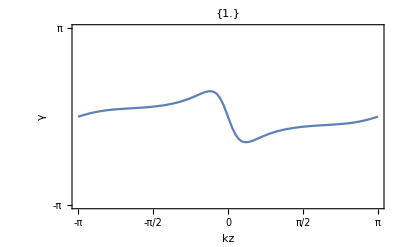

```mathematica
ClearAll["Global`*"]
k0=0.5;
t=1;(*hopping amplitude*)
m=1;(*mass amplitude*)
numOfstep=50;(*number of iterating steps*)
H[kx_,ky_,kz_,t_,m_,k0_]:=(m(2-Cos[ky]-Cos[kz])+2t(Cos[kx]-Cos[k0]))PauliMatrix[1]+2 t Sin[ky]PauliMatrix[2]+2t Sin[kz]PauliMatrix[3];(*Hamiltonian*)
(*H[kx_,ky_,kz_,t_,m_,k0_]:=kx PauliMatrix[1]+ky PauliMatrix[2]+kz PauliMatrix[3]*)

posi[kx_,ky_,kz_]:=Position[Eigensystem[
H[kx,ky,kz,t,m,k0]][[1]],_?Negative][[1,1]];

eigenvec[kx_,ky_,kz_]:=
{Normalize[Transpose[N@
Eigensystem[
H[kx,ky,kz,t,m,k0]]//Transpose][[2,posi[kx,ky,kz]]]]}//Transpose

coupMatrix[kx_,ky_,kz_]:=Dot[eigenvec[kx,ky,kz],eigenvec[kx,ky,kz]//ConjugateTranspose];(*coupling matrix*)

kx=1;
Plot[
vecInitial=eigenvec[kx,-Pi,kz];
-Im@Dot[vecInitial//ConjugateTranspose,
Dot@@
Table[coupMatrix[kx,ky,kz],{ky,-Pi,Pi,2Pi/numOfstep}](*prod of coupling mat (ky=-Π -> ky=Π)*)
,vecInitial][[1,1]],{kz,-Pi,Pi},PlotPoints->100,MaxRecursion->0,Frame->True,FrameLabel->{"kz","γ"},FrameTicks->{{-Pi,-Pi/2,0,Pi/2,Pi},{-Pi,Pi}},PlotRange->{-Pi,Pi},PlotLabel->{N@kx}]
```

```mathematica
kx0=0;
ky0=Pi;
Eigenvalues[Transpose[coupMatrix[kx0,ky0,0]].H[kx0,ky0,0,t,m,k0].Transpose[coupMatrix[kx0,ky0,0]]]
Eigenvalues[H[kx0,ky0,0,t,m,k0]]//N
```

{-2.24483,0.}

{-2.24483,2.24483}

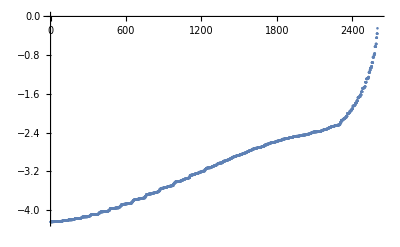

```mathematica
Sort[Table[Eigenvalues[coupMatrix[0,kx,ky].H[0,kx,ky,t,m,k0].coupMatrix[0,kx,ky]][[1]],{ky,-Pi,Pi,2Pi/numOfstep},{kx,-Pi,Pi,2Pi/numOfstep}]//Flatten]//ListPlot
```

```mathematica
ClearAll["Global`*"]
c[kx0_]:=
Module[{kx=kx0,
k0=1,
m=1,
t=1},
v[kx_,ky_,kz_,k0_,m_,t_]:=Normalize[{2t(Cos[kx]-Cos[k0])+m(2-Cos[ky]-Cos[kz]),2t Sin[ky],2t Sin[kz]}];
NIntegrate[Dot[v[kx,ky,kz,k0,m,t],Cross[D[v[kx,ky,kz,k0,m,t],ky],D[v[kx,ky,kz,k0,m,t],kz]]],{ky,-Pi,Pi},{kz,-Pi,Pi},AccuracyGoal->3]/Pi/4]
```

```mathematica
Module[{t=1,kx=0},
Manipulate[
ParametricPlot3D[{2t(Cos[kx]-Cos[k0])+m(2-Cos[ky]-Cos[kz]),2t Sin[ky],2t Sin[kz]},{ky,-Pi,Pi},{kz,-0.1,max},PlotRange->{{0,8}}],{k0,-Pi,Pi},{max,0,2Pi},{m,-2,2}]]
```

```mathematica
eigenvec[kx_,ky_,kz_]:=
Transpose[N@
Sort[
Eigensystem[
H[kx,ky,kz,t,m,k0]]//Transpose,#1[[1]]<#2[[1]]&]][[2,1]]
eigenvec[0,Pi,0]
```

{-1.,1.}

{{2.9194,{1.,1.}},{-2.9194,{-1.,1.}}}

```mathematica
N@Eigensystem[
H[0,Pi,0,t,m,k0]]//First
```

{2.9194,-2.9194}